```mathematica
Clear["Global`*"]
```

```mathematica
SeedRandom[1235];
```

```mathematica
n=1000;
k=2;
z=RandomVariate[NormalDistribution[],n];
β=RandomVariate[UniformDistribution[{1,3}],k];
x=Table[β⟦j⟧ z+RandomVariate[NormalDistribution[],n],{j,1,k}];
Correlation[xᵀ]
```

(1. | 0.802334
0.802334 | 1.)

```mathematica
c=CholeskyDecomposition[Correlation[xᵀ]]ᵀ
```

(1. | 0.
0.802334 | 0.596876)

```mathematica
NMinimize[Variance[x⟦1⟧-h x⟦2⟧],{h,-1,2}]
```

{2.03006,{h→0.871685}}

```mathematica
Covariance[x⟦1⟧,x⟦2⟧]/Variance[x⟦2⟧]
```

0.871685

```mathematica
NMinimize[-Quantile[x⟦1⟧-h x⟦2⟧,0.01],{h,-1,2}]
```

Quantile::rectn: Rectangular array of real numbers is expected at position 1 in Quantile[{-0.876536-1.6021 h,-2.07016+1.98218 h,3.86051-1.78158 h,«5»,1.00595-1.34604 h,2.31419-1.00313 h,«990»},0.01].

General::stop: Further output of Quantile::rectn will be suppressed during this calculation.

{3.33325,{h→0.852936}}

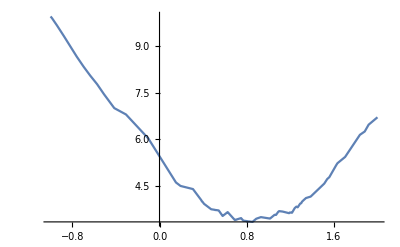

```mathematica
Plot[-Quantile[x⟦1⟧-h x⟦2⟧,0.01],{h,-1,2}]
```

```mathematica
n=200;
k=2;
z=RandomVariate[NormalDistribution[],n];
β=RandomVariate[UniformDistribution[{1,3}],k];
y=Table[β⟦j⟧ z+RandomVariate[NormalDistribution[],n],{j,1,k}];
```

```mathematica
Correlation[yᵀ]
```

(1. | 0.855445
0.855445 | 1.)

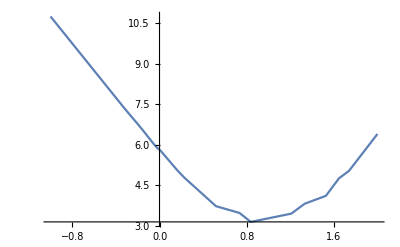

```mathematica
Plot[-Quantile[y⟦1⟧-h y⟦2⟧,0.01],{h,-1,2}]
```